```mathematica
(* Jarek Duda, preprint: https://arxiv.org/abs/2112.12557 , article:  *)
```

```mathematica
(* Laplacian for Poisson equation to find potential from electron MERW stationary probability distribution *)
findpois:=(pois={};Vl=Vr=Table[0,nm];rho0=1./nm;
Do[ip=Mod[i+1,n];im=Mod[i-1,n];jp=Mod[j+1,m];jm=Mod[j-1,m];c=m*i+j+1;
AppendTo[pois,{c,c}->4-If[(j==0)||(j==m-1),1,0]];AppendTo[pois,{c,m*ip+j+1}->-1];AppendTo[pois,{c,m*im+j+1}->-1];
If[j>0,AppendTo[pois,{c,m*i+jm+1}->-1]];
If[j<m-1,AppendTo[pois,{c,m*i+jp+1}->-1]];
If[j==0,Vl[[c]]=1];If[j==m-1,Vr[[c]]=1];
(*If[j>0,AppendTo[pois,{c,m*i+j}->-1],bVl[[c]]=1];If[j<m-1,AppendTo[pois,{c,m*i+j+2}->-1],bVr[[c]]=1];*)
,{i,0,n-1},{j,0,m-1}];Vgr=-Table[Range[1.,m]/m,n];
pois=SparseArray[pois];);
(* find potential from electron MERW stationary probability distribution *)
findV:=(V=Partition[LinearSolve[pois,-gamma(Flatten[pd]-rho0)],m]+Vgr*Vd);
(* generate diagonal M terms: df - default, dp - defect probability, ds - defect strength *)
finddef:=(SeedRandom[seed];ne=nd=0;M0=Table[0,nm];rp=Length[dps]/m;rs=Length[dss]/m;
dpt=Table[dps[[Ceiling[z*rp]]],{z,m}];dst=Table[dss[[Ceiling[z*rs]]],{z,m}];
defs=Table[If[RandomReal[]>dpt[[j+1]],df,dst[[j+1]]],{i,0,n-1},{j,0,m-1}];
M0=Transpose[{Range[nm],Range[nm],Flatten[defs]}]);
(* find MERW matrix, eigenvectors, stationary probability distribution pd *)
MERW:=(ne=0;Me=Table[0,4nm];
Ju=Exp[beta*(V-RotateRight[V,1])];t=V-RotateLeft[V,{0,1}]; Do[t[[i,-1]]=0.,{i,n}];   (* 0 boundary diff *)
Jr=Exp[beta*t];Juf=Flatten[Ju];Jrf=Flatten[Jr];Jui=1/Juf;Jri=1/Jrf;
Do[c=m*i+j+1;cip=m*Mod[i+1,n]+j+1;cjp=m*i+Mod[j+1,m]+1;
Me[[++ne]]={c,cjp,Jrf[[c]]};Me[[++ne]]={cjp,c,Jri[[c]]};
Me[[++ne]]={c,cip,Juf[[c]]};Me[[++ne]]={cip,c,Jui[[c]]};
,{i,0,n-1},{j,0,m-1}];
M=SparseArray[Map[{#[[1]],#[[2]]}->#[[3]]&,MM=Join[M0,Me[[1;;ne]]]]];
(* MERW *)
er=Abs[Eigensystem[M,1, Method -> {Arnoldi, MaxIterations->100000(*,Shift->(M//Total//Total)/nm*)}]];
lam=er[[1,1]];er=er[[2,1]];
el=Abs[Eigensystem[Transpose[M],1,Method -> {Arnoldi, MaxIterations->100000,Shift->lam}]][[2,1]];
pd=er*el;pd=Partition[pd,m]/Total[pd]);
(* calculate current as sum_y Pr(x,y) S((x,y)->(x+1,y)) - Pr(x+1,y) S((x+1,y)->(x,y)) *)
flow:=(eT=Partition[er,m];erd=RotateLeft[eT,1];eru=RotateRight[eT,1];err=RotateLeft[eT,{0,1}];erl=RotateRight[eT,{0,1}];
Jd=RotateLeft[1/Ju,1];Jl=RotateRight[1/Jr,{0,1}];
er1=1/eT/lam;Pu=Ju*eru*er1;Pd=Jd*erd*er1;Pl=Jl*erl*er1;Pr=Jr*err*er1;
fl=Map[Total,Transpose[pd*Pr]]-RotateLeft[Map[Total,Transpose[pd*Pl]],1]);
drawdef:=(defm=defp={};
Do[If[defs[[i,j]]!=df,cb=Ball[{j-0.5,i-0.5},0.2];If[defs[[i,j]]>df,AppendTo[defp,cb],AppendTo[defm,cb]]],{i,n},{j,m}];
Graphics[{Opacity[0.3],Red,defm,Green,defp}]);
arrows:=(fm=len*Partition[Transpose[{Flatten[pd(Pr-Pl)],-Flatten[pd(Pu-Pd)]}],m];
Graphics[{Blue,Thickness[0.001],Arrowheads[Small],Flatten[Table[Arrow[{{j,i},fm[[i,j]]+{j,i}}-0.5],{i,n},{j,m}]]}])
```

```mathematica
(* main calculation with plot I(U), takes a few minutes, reduce {k,100} to shorten *)
```

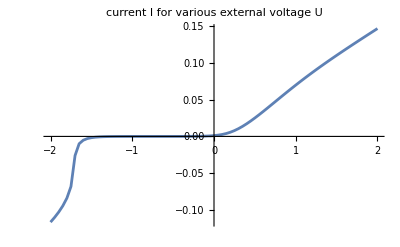

```mathematica
n=20;beta=10;gamma=1.;m=3*n;nm=n*m;seed=3;findpois;
len=10nm;rn=2.;Vds=Range[-rn,rn,rn/40];Vss=pls=pds=pst=pst1={};dv={};
dps={0.1,0.1};df=0.5;dss={0.,1.};
finddef;
pl=Table[{Vd,V0=V=Vgr*Vd;Do[MERW;findV,{k,100}];(* main loop MERW -> Poisson repeat  *)
pV=V;AppendTo[dv,Norm[pV-V]];MERW;
AppendTo[Vss,Map[Mean,Transpose[V-V0]]];AppendTo[pds,Map[Total,Transpose[pd]]];
flow;AppendTo[pst,Mean[Mean[1-Pu-Pd-Pr-Pl]]];
AppendTo[pst1,Map[Mean,Transpose[1-Pu-Pd-Pr-Pl]]];
AppendTo[pls,Show[ArrayPlot[pd,ImageSize->Large,Frame->False],drawdef,arrows]];Total[fl]},{Vd,Vds}];
ListPlot[{pl},Joined->True,PlotRange->All,PlotLabel->"current I for various external voltage U"]
```

```mathematica
(* densities for external voltages: *)
```

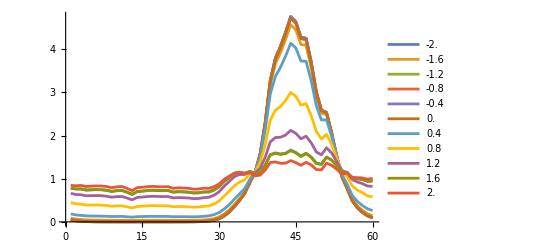

```mathematica
ListPlot[pds[[1;;-1;;8]]*m,Joined->True,PlotLegends->Vds[[1;;-1;;8]]]
```

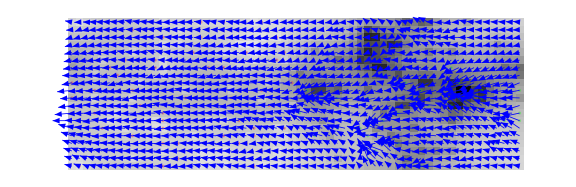
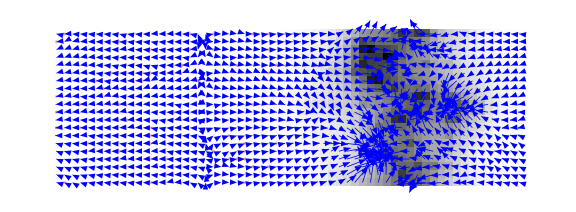
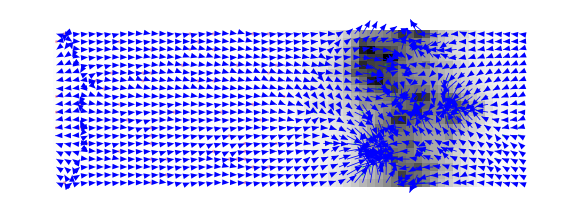
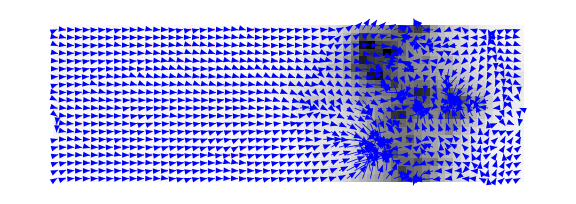
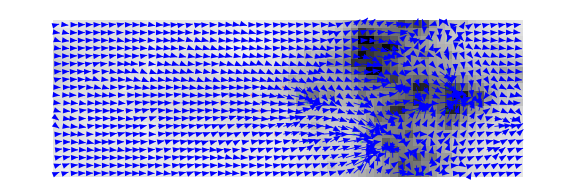
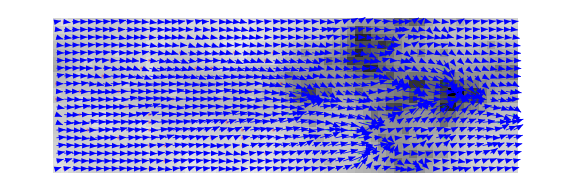
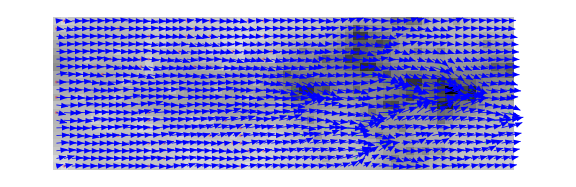
U = -2. | -Graphics-
U = -1. | -Graphics-
U = 0. | -Graphics-
U = 0.5 | -Graphics-
U = 1. | -Graphics-
U = 1.5 | -Graphics-
U = 2. | -Graphics-

```mathematica
Grid[Table[{Rotate[Row[{Style["U",Italic]," = ",Vds[[i]]}],Pi/2],pls[[i]]},{i,{1,21,41,51,61,71,81}}],Spacings->{0,-1.5}]
```

```mathematica
(* potential *)
```

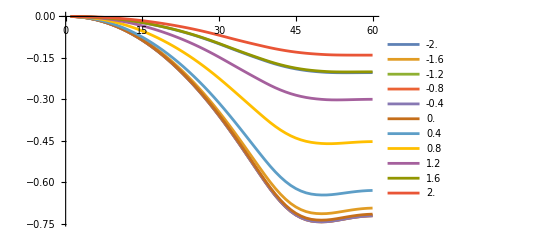

```mathematica
Vs=Table[vv-vv[[1]],{vv,Vss[[1;;-1;;8]]}];ListPlot[Vs,Joined->True,PlotLegends->Vds[[1;;-1;;8]]]
```